## Белко Владислав, ПО-5

Лабораторная работа №2.  Символьные вычисления в системе Mathematica

## Задание 1. I.1

Придумайте и определите...

```mathematica
bv1=(42 (x^2-y^4))/((4 x+2) (x^4-y^2))+x^2-y^2+4(x-y);
```

```mathematica
Expand[bv1] (*раскрывает скобки отдельных выражений и всё в виде суммы*)
```

4 x+x^2-4 y-y^2+(42 x^2)/((2+4 x) (x^4-y^2))-(42 y^4)/((2+4 x) (x^4-y^2))

```mathematica
ExpandAll[bv1] (*раскрывает скобки во всех выр-х(знаметаль) и всё в виде суммы*)
```

4 x+x^2-4 y-y^2+(42 x^2)/(2 x^4+4 x^5-2 y^2-4 x y^2)-(42 y^4)/(2 x^4+4 x^5-2 y^2-4 x y^2)

```mathematica
Together[bv1] (*общий знаменатель*)
```

(21 x^2+4 x^5+9 x^6+2 x^7-4 x^4 y-8 x^5 y-4 x y^2-9 x^2 y^2-2 x^3 y^2-x^4 y^2-2 x^5 y^2+4 y^3+8 x y^3-20 y^4+2 x y^4)/((1+2 x) (x^4-y^2))

```mathematica
Apart[bv1](*разложение рационального выражения на неполные дроби*)
```

(x (4+9 x+2 x^2+21 x^3))/(1+2 x)-4 y-(2 (-10+x) y^2)/(1+2 x)+(21 (-1+x^6))/(2 (1+2 x) (-x^2+y))-(21 (-1+x^6))/(2 (1+2 x) (x^2+y))

```mathematica
Cancel[bv1](*отменяет общие множители в числителе и знаменателе*)
```

x^2+4 (x-y)-y^2+(21 (x^2-y^4))/((1+2 x) (x^4-y^2))

```mathematica
Simplify[bv1](*пытается упростить*)
```

x^2+4 (x-y)-y^2+(21 (x^2-y^4))/((1+2 x) (x^4-y^2))

## I.2

```mathematica
bv2=Numerator[Together[bv1]]
```

21 x^2+4 x^5+9 x^6+2 x^7-4 x^4 y-8 x^5 y-4 x y^2-9 x^2 y^2-2 x^3 y^2-x^4 y^2-2 x^5 y^2+4 y^3+8 x y^3-20 y^4+2 x y^4

```mathematica
Collect[bv2,x] (*группирует выражение рядом с одинаковой степенью х/у*)
Collect[bv2,y]
```

9 x^6+2 x^7-2 x^3 y^2+4 y^3-20 y^4+x^2 (21-9 y^2)+x^5 (4-8 y-2 y^2)+x^4 (-4 y-y^2)+x (-4 y^2+8 y^3+2 y^4)

21 x^2+4 x^5+9 x^6+2 x^7+(-4 x^4-8 x^5) y+(-4 x-9 x^2-2 x^3-x^4-2 x^5) y^2+(4+8 x) y^3+(-20+2 x) y^4

```mathematica
Exponent[bv2,x]
```

7

```mathematica
Coefficient[bv2,x,Exponent[bv2,x]]
Coefficient[bv2,x,2]
```

2

21-9 y^2

```mathematica
CoefficientList[bv2,x]
```

{4 y^3-20 y^4,-4 y^2+8 y^3+2 y^4,21-9 y^2,-2 y^2,-4 y-y^2,4-8 y-2 y^2,9,2}

## Задание 2.

1. С помощью функции D вычислите производную функции x^ncos x.

```mathematica
D[x^n Cos[x],x]
```

```mathematica
n x^(-1+n) Cos[x]-x^n Sin[x]
```

2. Вычислите следующие производные

```mathematica
D[a x^3+2 x^2,x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5 x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[ x^3 y^2+3 x^2,{x,3},{y,2}]
```

12

3. Используя функцию Integrate, вычислите интеграл

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
∫1/(x^2-1)ⅆx
```

1/2 Log[1-x]-1/2 Log[1+x]

4. Вычислите интегралы, а затем	 продифференцируйте полученные выражения и убедитесь в том,
что получаемые результаты совпадают с подынтегральными выражениями.

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2],x]] (*собирает отдельные части под один знаменатель*)
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]] (*раскрывает все скобки*)
```

1/(1+x^3)

```mathematica
Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]]] (*без раскрытия*)
```

1/6 (2 √3 ArcTan[(-1+2 x)/(√3)]+2 Log[1+x]-Log[1-x+x^2])

5. Вычислите определённый интеграл.

```mathematica
Integrate[5x-2√x+32/x^3,{x,1,4}]
```

259/6

6. Вычислите интегралы.

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}]
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
%//N
```

1.05753

```mathematica
Hypergeometric2F1[-1/3,1/4,5/4,-1](*Гаус*)
```

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

```mathematica
Задание 3.
```

1. Используя функцию Solve	 решить уравнение ax^4+ x^2 + 3 = 0;

```mathematica
Solve[ax^4+x^2+3==0,x]
```

{{x→-√(-3-ax^4)},{x→√(-3-ax^4)}}

2. Найти точное решение системы уравнений

```mathematica
NSolve[x^2+y==1 && y^2-x^2==2,{x,y}]
```

{{x→-1.81735,y→-2.30278},{x→0.-0.550251 ⅈ,y→1.30278},{x→0.+0.550251 ⅈ,y→1.30278},{x→1.81735,y→-2.30278}}

3. Решить систему уравнений.

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

4. Найдите общие решения дифференциальных уравнений, используя функцию DSolve.

```mathematica
bv41=DSolve[y'[x]-y[x]Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
bv42 = DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

{{y[x]→1/(cosx tgx)+ⅇ^(-tgx x) C[1]}}

5. Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде.

```mathematica
DSolve[y''[x]-y'[x]+x y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}

```mathematica
bv51=DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], x]// FullSimplify
```

{{y[x]→1/2 ⅇ^(x/2) π (-((AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4]))}}

```mathematica
bv52=NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x],{x,-10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

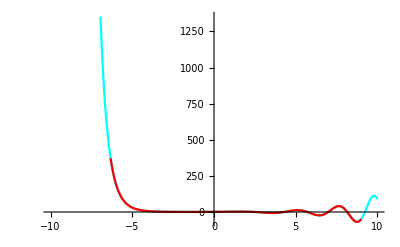

```mathematica
Show[Plot[bv51[[1,1,2]],{x,-10,10},PlotStyle->{Cyan}], Plot[bv52[[1, 1, 2]], {x, -9, 9},PlotStyle->{Red}]]
```